```mathematica
8.46^2+4.27^2+3.19^2
```

99.9806

```mathematica
(*data = Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output.csv"],{2}];*)
output= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],3,4],5]])&/@data;
chart=Table[Count[output,i],{i,0,5}]
energychart={TotalUsedEnergy[data], TotalUntouchedEnergy[data],TotalEscapedEnergy[data],TotalEnergy[data]-TotalOutput[data]}
PieChart[chart,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Absorbed by target", "Useful", "Absorbed by LC"}, ChartStyle->"DarkRainbow"]
PieChart[energychart,ChartLegends->{"Output", "Untouched", "Escaped", "Lost"}, ChartStyle->{Yellow,Green, Blue, Gray}]
```

{24702,59011,10421,4896,950,20}

{10.2671,54.8933,105.166,28.7376}

-Graphics-

-Graphics-

```mathematica
{10.267077157664886,78.0511111111111,78.0511111111111,28.73758499584386}
```

{10.2671,78.0511,78.0511,28.7376}

```mathematica
data[[All,-1]]
```

{{pos=(2.60, -0.84, 9.62), dir=(0.26, -0.14, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(9.44, 3.27, -0.40), dir=(0.93, 0.33, -0.13), nm=569.03, alive=True), <Event.EXIT: 6>},{pos=(-7.90, -5.27, 3.13), dir=(-0.68, -0.71, 0.19), nm=576.93, alive=True), <Event.EXIT: 6>},{pos=(-8.05, 0.43, 5.91), dir=(-0.84, 0.09, 0.53), nm=594.99, alive=True), <Event.EXIT: 6>},{pos=(5.75, -2.20, -7.88), dir=(0.50, -0.31, -0.81), nm=520.26, alive=True), <Event.EXIT: 6>},{pos=(4.00, 2.88, 8.70), dir=(0.42, 0.24, 0.87), nm=532.79, alive=True), <Event.EXIT: 6>},{pos=(0.21, 4.29, 1.05), dir=(0.34, 0.94, 0.07), nm=647.02, alive=True), <Event.ABSORB: 3>},{pos=(-6.10, -6.89, 3.92), dir=(-0.68, -0.65, 0.34), nm=559.01, alive=True), <Event.EXIT: 6>},{pos=(9.77, 0.14, 2.15), dir=(0.92, 0.37, 0.11), nm=604.19, alive=True), <Event.EXIT: 6>},{pos=(-2.77, 4.95, -8.24), dir=(-0.22, 0.54, -0.81), nm=546.07, alive=True), <Event.EXIT: 6>},{pos=(8.12, -1.46, 5.65), dir=(0.87, 0.00, 0.49), nm=628.90, alive=True), <Event.EXIT: 6>},{pos=(-6.48, 6.12, 4.54), dir=(-0.69, 0.62, 0.36), nm=578.09, alive=True), <Event.EXIT: 6>},{pos=(-3.45, 1.92, 9.19), dir=(-0.35, 0.12, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(9.07, -1.30, 4.01), dir=(0.93, -0.17, 0.32), nm=546.05, alive=True), <Event.EXIT: 6>},{pos=(0.38, -6.99, -7.14), dir=(0.01, -0.63, -0.78), nm=520.76, alive=True), <Event.EXIT: 6>},{pos=(5.68, 6.65, 4.85), dir=(0.62, 0.65, 0.44), nm=565.75, alive=True), <Event.EXIT: 6>},{pos=(2.31, 1.85, 9.55), dir=(0.22, 0.25, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-0.54, 3.91, 1.24), dir=(-0.69, 0.50, 0.51), nm=597.27, alive=True), <Event.ABSORB: 3>},{pos=(6.94, 0.11, -7.20), dir=(0.62, -0.19, -0.76), nm=679.31, alive=True), <Event.EXIT: 6>},{pos=(-1.88, -3.34, 9.24), dir=(-0.20, -0.17, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(3.67, 0.39, 9.29), dir=(0.37, -0.02, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(2.87, 3.36, 8.97), dir=(0.31, 0.16, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-3.46, 1.60, 9.25), dir=(-0.35, 0.10, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-2.62, 0.91, 9.61), dir=(-0.26, -0.04, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-6.70, -7.38, 0.77), dir=(-0.70, -0.71, -0.03), nm=584.07, alive=True), <Event.EXIT: 6>},{pos=(4.85, -8.27, -2.85), dir=(0.43, -0.83, -0.36), nm=532.17, alive=True), <Event.EXIT: 6>},{pos=(-2.34, -0.38, 9.72), dir=(-0.23, -0.08, 0.97), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(1.32, -1.29, 9.83), dir=(0.13, -0.24, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-2.85, -3.17, 9.05), dir=(-0.29, -0.25, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(0.29, 4.03, 9.15), dir=(0.04, 0.30, 0.95), nm=510.64, alive=True), <Event.EXIT: 6>},{pos=(-3.28, 3.07, 8.93), dir=(-0.34, 0.14, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-0.16, 4.03, 0.79), dir=(-0.50, 0.77, -0.40), nm=545.82, alive=True), <Event.ABSORB: 3>},{pos=(5.36, 6.41, 5.50), dir=(0.55, 0.70, 0.46), nm=618.29, alive=True), <Event.EXIT: 6>},{pos=(2.31, -0.78, 9.70), dir=(0.23, -0.12, 0.97), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-3.73, -1.15, 9.20), dir=(-0.38, 0.06, 0.92), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-2.74, 2.68, 9.24), dir=(-0.28, 0.07, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-0.42, -2.19, -9.75), dir=(-0.03, -0.16, -0.99), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(2.99, -2.73, 9.14), dir=(0.31, -0.09, 0.95), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(3.78, 5.56, 7.40), dir=(0.35, 0.70, 0.62), nm=557.48, alive=True), <Event.EXIT: 6>},{pos=(1.64, -9.85, 0.51), dir=(0.29, -0.95, -0.08), nm=526.66, alive=True), <Event.EXIT: 6>},{pos=(-0.14, -0.17, 10.00), dir=(-0.02, 0.15, 0.99), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-2.86, 0.99, 9.53), dir=(-0.29, 0.02, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-4.71, -1.16, -8.74), dir=(-0.44, -0.21, -0.87), nm=560.30, alive=True), <Event.EXIT: 6>},{pos=(2.96, -1.46, 9.44), dir=(0.33, -0.14, 0.93), nm=543.40, alive=True), <Event.EXIT: 6>},{pos=(9.48, 1.35, -2.88), dir=(0.91, -0.16, -0.38), nm=595.34, alive=True), <Event.EXIT: 6>},{pos=(-3.14, 3.02, 9.00), dir=(-0.32, 0.16, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-5.10, 1.54, 8.46), dir=(-0.53, 0.25, 0.81), nm=630.47, alive=True), <Event.EXIT: 6>},{pos=(8.64, -3.42, -3.70), dir=(0.87, -0.07, -0.48), nm=577.41, alive=True), <Event.EXIT: 6>},{pos=(0.62, 0.50, -9.97), dir=(0.07, -0.01, -1.00), nm=571.44, alive=True), <Event.EXIT: 6>},{pos=(-0.37, -2.28, -9.73), dir=(-0.03, -0.07, -1.00), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(8.81, -1.01, 4.63), dir=(0.92, -0.08, 0.39), nm=533.97, alive=True), <Event.EXIT: 6>},{pos=(1.82, 1.20, 9.76), dir=(0.18, 0.30, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(3.14, 3.17, 8.95), dir=(0.32, 0.17, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(4.54, -2.86, 8.44), dir=(0.41, -0.57, 0.71), nm=612.85, alive=True), <Event.EXIT: 6>},{pos=(-6.17, 7.56, 2.21), dir=(-0.65, 0.75, 0.13), nm=518.94, alive=True), <Event.EXIT: 6>},{pos=(-5.94, -0.05, 8.05), dir=(-0.63, -0.07, 0.77), nm=547.63, alive=True), <Event.EXIT: 6>},{pos=(-0.16, 4.31, 0.76), dir=(-0.23, 0.93, -0.29), nm=650.84, alive=True), <Event.ABSORB: 3>},{pos=(1.94, 4.44, -8.75), dir=(0.15, 0.50, -0.85), nm=556.86, alive=True), <Event.EXIT: 6>},{pos=(-9.25, -3.35, -1.81), dir=(-0.91, -0.31, -0.28), nm=675.54, alive=True), <Event.EXIT: 6>},{pos=(-2.70, -1.73, 9.47), dir=(-0.27, -0.05, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(9.98, -0.47, -0.52), dir=(0.97, 0.17, -0.15), nm=544.83, alive=True), <Event.EXIT: 6>},{pos=(-7.03, -5.88, -4.01), dir=(-0.73, -0.42, -0.54), nm=643.44, alive=True), <Event.EXIT: 6>},{pos=(-3.27, -7.26, -6.04), dir=(-0.40, -0.41, -0.82), nm=630.77, alive=True), <Event.EXIT: 6>},{pos=(-4.28, -6.22, -6.56), dir=(-0.40, -0.53, -0.75), nm=593.79, alive=True), <Event.EXIT: 6>},{pos=(-2.60, -2.59, 9.30), dir=(-0.26, -0.12, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-8.34, 5.44, -0.95), dir=(-0.86, 0.47, -0.21), nm=524.53, alive=True), <Event.EXIT: 6>},{pos=(0.97, 2.29, 9.68), dir=(0.10, 0.03, 0.99), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-4.49, 5.54, 7.01), dir=(-0.51, 0.45, 0.73), nm=549.69, alive=True), <Event.EXIT: 6>},{pos=(-3.74, 8.10, -4.52), dir=(-0.33, 0.79, -0.52), nm=526.45, alive=True), <Event.EXIT: 6>},{pos=(-1.60, -3.12, -9.36), dir=(-0.16, -0.10, -0.98), nm=679.85, alive=True), <Event.EXIT: 6>},{pos=(2.78, -0.81, 9.57), dir=(0.27, -0.24, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-2.91, -0.32, -9.56), dir=(-0.28, 0.07, -0.96), nm=513.54, alive=True), <Event.EXIT: 6>},{pos=(2.94, -1.04, 9.50), dir=(0.29, 0.02, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(1.09, -0.81, 9.91), dir=(0.11, -0.01, 0.99), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-3.17, -0.07, 9.48), dir=(-0.32, -0.17, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(0.53, -3.70, 9.28), dir=(0.05, -0.25, 0.97), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-3.53, 0.36, 9.35), dir=(-0.35, -0.09, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(8.06, 4.18, 4.20), dir=(0.91, 0.21, 0.37), nm=584.35, alive=True), <Event.EXIT: 6>},{pos=(-1.72, -7.73, -6.11), dir=(-0.16, -0.68, -0.71), nm=534.34, alive=True), <Event.EXIT: 6>},{pos=(-2.02, 8.24, -5.30), dir=(-0.17, 0.80, -0.57), nm=631.31, alive=True), <Event.EXIT: 6>},{pos=(-8.00, -1.56, -5.80), dir=(-0.73, -0.23, -0.64), nm=624.38, alive=True), <Event.EXIT: 6>},{pos=(3.23, 0.71, 9.44), dir=(0.32, 0.17, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(3.48, -0.95, 9.33), dir=(0.35, -0.07, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(7.96, 5.67, -2.12), dir=(0.70, 0.67, -0.27), nm=500.36, alive=True), <Event.EXIT: 6>},{pos=(-2.88, -2.95, 9.11), dir=(-0.30, -0.16, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(2.39, -9.70, 0.42), dir=(0.37, -0.93, -0.09), nm=604.16, alive=True), <Event.EXIT: 6>},{pos=(-2.20, 6.18, 7.55), dir=(-0.24, 0.53, 0.81), nm=581.92, alive=True), <Event.EXIT: 6>},{pos=(-2.78, 0.03, 9.61), dir=(-0.27, 0.02, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-3.21, 8.88, -3.29), dir=(-0.26, 0.90, -0.35), nm=501.59, alive=True), <Event.EXIT: 6>},{pos=(2.92, 0.95, 9.52), dir=(0.33, 0.06, 0.94), nm=598.42, alive=True), <Event.EXIT: 6>},{pos=(0.86, -4.57, -8.85), dir=(0.07, -0.32, -0.94), nm=536.18, alive=True), <Event.EXIT: 6>},{pos=(0.26, 4.43, 0.14), dir=(-0.08, 0.94, 0.33), nm=584.85, alive=True), <Event.ABSORB: 3>},{pos=(1.48, 8.38, -5.25), dir=(0.13, 0.74, -0.66), nm=592.41, alive=True), <Event.EXIT: 6>},{pos=(1.19, -8.71, -4.77), dir=(0.14, -0.71, -0.69), nm=633.89, alive=True), <Event.EXIT: 6>},{pos=(-6.61, 3.95, 6.38), dir=(-0.75, 0.30, 0.60), nm=580.44, alive=True), <Event.EXIT: 6>},{pos=(2.64, 2.50, 9.31), dir=(0.27, 0.12, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-2.79, 3.13, 9.08), dir=(-0.28, 0.25, 0.92), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(-6.97, 0.75, -7.13), dir=(-0.64, 0.04, -0.77), nm=544.73, alive=True), <Event.EXIT: 6>},{pos=(2.60, -2.40, 9.35), dir=(0.26, -0.12, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>},{pos=(4.25, -8.23, 3.78), dir=(0.62, -0.67, 0.41), nm=544.26, alive=True), <Event.EXIT: 6>}}

```mathematica
0=No interaction
1=Interaction but escape
2= Interaction without wavelength change
3= Absorbtion by PPT
4= Absorbtion by YAG
```

```mathematica
output= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,1],2])&/@data
```

{0,1,1,1,1,1,2,1,1,1,1,1,0,1,1,1,0,2,1,1,0,0,0,0,1,1,0,1,0,1,0,2,1,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,2,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,0,0,1,0,1,1,0,1,1,1,2,1,1,1,0,0,1,0,1}

```mathematica
test=data[[1,-1]]
CleanOutput[test]
```

(Ray(pos=(2.60, -0.84, 9.62), dir=(0.26, -0.14, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>)

{pos=(2.60, -0.84, 9.62), dir=(0.26, -0.14, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>}

```mathematica
CleanOutput[str_]:=StringSplit[StringDrop[StringDelete[StringDelete[str, "(Ray("],"[Ray("],-1],","]
```

```mathematica
data1=Map[CleanOutput, data, {2}];
data1[[1,-1]]
```

{pos=(2.60, -0.84, 9.62), dir=(0.26, -0.14, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>}

```mathematica
data1[[1,-1,-1]]
```

<Event.EXIT: 6>

```mathematica
StringTake[data1[[1,-1,-1]],{-2}]
```

6

```mathematica
StringTake[data[[1,-1,-1]],{-2}]
```

6

```mathematica
Length[data[[3]]]
```

35

```mathematica
RemovePosition[str_]:=ToExpression[StringDelete[StringDelete[str,"pos=("],")"]]
CheckSphere[list_]:= Total[(list-{0,4.5,1})^2]≤1
```

```mathematica
abs=DeleteCases[(If[StringTake[#[[-1,-1]],{-2}]=="3",
#[[-1]],0])&/@data,0]
```

{{pos=(0.21, 4.29, 1.05), dir=(0.34, 0.94, 0.07), nm=647.02, alive=True), <Event.ABSORB: 3>},{pos=(-0.54, 3.91, 1.24), dir=(-0.69, 0.50, 0.51), nm=597.27, alive=True), <Event.ABSORB: 3>},{pos=(-0.16, 4.03, 0.79), dir=(-0.50, 0.77, -0.40), nm=545.82, alive=True), <Event.ABSORB: 3>},{pos=(-0.16, 4.31, 0.76), dir=(-0.23, 0.93, -0.29), nm=650.84, alive=True), <Event.ABSORB: 3>},{pos=(0.26, 4.43, 0.14), dir=(-0.08, 0.94, 0.33), nm=584.85, alive=True), <Event.ABSORB: 3>}}

```mathematica
abs1=RemovePosition[#1]&/@#[[1;;3]]&/@abs
```

{{0.21,4.29,1.05},{-0.54,3.91,1.24},{-0.16,4.03,0.79},{-0.16,4.31,0.76},{0.26,4.43,0.14}}

```mathematica
CheckSphere[abs1[[1]]]
```

True

```mathematica
CheckSphere[#]&/@(RemovePosition[#]&/@#[[1;;3]]&/@abs)
```

abs

```mathematica
output== {0,1,1,1,1,1,2,1,1,1,1,1,0,1,1,1,0,2,1,1,0,0,0,0,1,1,0,1,0,1,0,2,1,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,2,1,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,0,0,1,0,1,1,0,1,1,1,2,1,1,1,0,0,1,0,1}
```

True

```mathematica
StringTake[#[[All,-1]],{-2}]&/@data
```

{{0,6},{0,2,5,1,5,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,1,1,1,1,1,5,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,2,6},{0,2,5,2,6},{0,2,5,1,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,3},{0,2,5,1,2,6},{0,2,5,1,5,1,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,1,1,2,6},{0,2,5,5,2,6},{0,2,5,1,1,1,1,1,5,2,6},{0,6},{0,2,5,1,2,6},{0,2,5,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,1,1,2,6},{0,6},{0,2,5,5,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,3},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,5,1,1,2,6},{0,2,2,6},{0,6},{0,6},{0,6},{0,6},{0,2,5,2,6},{0,2,5,1,2,6},{0,6},{0,2,2,6},{0,6},{0,2,5,2,6},{0,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,3},{0,2,5,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,2,2,6},{0,6},{0,6},{0,1,6},{0,6},{0,2,5,2,6},{0,2,5,1,1,1,1,1,2,6},{0,2,2,6},{0,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,5,2,6},{0,2,5,2,6},{0,2,5,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,6},{0,2,5,1,1,5,1,1,1,1,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,2,5,2,6},{0,1,6},{0,2,5,5,1,1,1,2,6},{0,2,2,6},{0,6},{0,2,5,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,2,5,2,6},{0,2,5,1,5,1,5,2,6},{0,2,5,1,1,1,1,1,1,1,2,5,1,2,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,3},{0,2,5,1,1,1,1,2,6},{0,2,5,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,6},{0,2,1,5,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,2,6},{0,2,5,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,6},{0,2,5,2,6},{0,6},{0,2,5,1,5,1,2,6},{0,2,2,6},{0,2,5,1,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,2,6},{0,2,5,1,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,2,6},{0,6},{0,2,5,2,6},{0,6},{0,2,2,6},{0,6},{0,2,2,6},{0,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,5,2,6},{0,2,5,2,6},{0,2,5,2,6},{0,2,5,1,2,6},{0,6},{0,6},{0,2,5,2,6},{0,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,2,6},{0,2,5,1,1,1,1,1,2,6},{0,6},{0,2,5,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,5,2,6},{0,2,5,2,6},{0,2,5,2,2,3},{0,2,5,1,2,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,2,6},{0,2,5,2,6},{0,6},{0,6},{0,2,5,1,2,6},{0,6},{0,2,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,1,1,1,1,1,1,2,6}}

```mathematica
mesh=Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\LC_18oct2020_tenth_of_length.stl"]
merged=Region`Mesh`MergeCells[mesh]
```

-Graphics3D-

-Graphics3D-

```mathematica
TotalEnergy[dataset_]:=Total[(1/ToExpression[StringTake[#[[1,-3]],-6]])&/@dataset]
TotalEnergy[data1]== 100/450
TotalEnergy[data]==100000/450
```

Total[data1]==2/9

Total[data]==2000/9

```mathematica
TotalOutput[dataset_]:= Total[(1/ToExpression[StringTake[#[[-1,-3]],-6]])&/@dataset]
TotalOutput[data1]/TotalEnergy[data1]
TotalOutput[data]/TotalEnergy[data]
```

1

1

```mathematica
TotalUsedEnergy[dataset_]:=Total[If[StringTake[#[[-1,-1]],{-2}]=="3", 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset]
TotalUsedEnergy[data1]/TotalEnergy[data1]
```

1

```mathematica
TotalUntouchedEnergy[dataset_]:=Total[If[StringTake[#[[-1,-1]],{-2}]=="6" &&Length[#]==2, 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset]
TotalUntouchedEnergy[data1]/TotalEnergy[data1]
```

1

```mathematica
TotalEscapedEnergy[dataset_]:=Total[If[StringTake[#[[-1,-1]],{-2}]=="6" &&AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&], 1/ToExpression[StringTake[#[[-1,-3]],-6]],0]&/@dataset]
```

```mathematica
data1= Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_10000.csv"],{2}];
output1= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],4,3],If[Count[StringTake[#[[All,-1]],{-2}],"5"]>0,If[Count[StringTake[#[[All,-1]],{-2}],"5"]>1,7,6],5]]])&/@data1;
chart1=Table[Count[output1,i],{i,0,7}]
energychart1={TotalUsedEnergy[data1], TotalUntouchedEnergy[data1],TotalEscapedEnergy[data1],TotalEnergy[data1]-TotalOutput[data1]}
PieChart[chart1,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Hit target but wrong wavelength", "Useful", "Absorbed by LC in first instance","Absorbed by LC after one emission", "Absorbed by LC after multiple emissions"}, ChartStyle->"DarkRainbow"]
PieChart[energychart1,ChartLegends->{"Output", "Untouched", "Escaped", "Lost"}, ChartStyle->{Yellow,Green, Blue, Gray}]
```

{2489,3721,1414,225,713,723,385,330}

{4.49364,5.53111,6.49791,2.55222}

-Graphics-

-Graphics-

```mathematica
(*CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])]&/@*)data1
```

{{{pos=(0.03, -0.79, 0.00), dir=(-0.19, 0.14, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.16, -0.65, 0.97), dir=(-0.10, 0.08, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.16, -0.64, 1.03), dir=(-0.19, 0.14, 0.97), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-1.84, 0.66, 9.81), dir=(-0.19, 0.14, 0.97), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.03, -1.55, 0.00), dir=(0.11, 0.36, 0.92), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.09, -1.16, 0.97), dir=(0.06, 0.20, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.09, -1.16, 1.02), dir=(-0.35, -0.29, 0.89), nm=576.46, alive=True), <Event.EMIT: 5>},{pos=(0.09, -1.16, 1.03), dir=(-0.64, -0.52, 0.56), nm=576.46, alive=True), <Event.TRANSMIT: 2>},{pos=(-5.58, -5.78, 5.95), dir=(-0.64, -0.52, 0.56), nm=576.46, alive=True), <Event.EXIT: 6>}},{{pos=(0.03, -0.99, 0.00), dir=(-0.11, 0.35, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.08, -0.63, 0.97), dir=(-0.06, 0.19, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.08, -0.62, 0.98), dir=(-0.06, 0.19, 0.98), nm=450.00, alive=True), <Event.ABSORB: 3>}},{{pos=(-0.01, 0.52, 0.00), dir=(-0.17, -0.21, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.18, 0.31, 0.97), dir=(-0.17, -0.21, -0.96), nm=450.00, alive=True), <Event.REFLECT: 1>},{pos=(-2.04, -2.05, -9.57), dir=(-0.17, -0.21, -0.96), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.02, 1.07, 0.00), dir=(0.31, 0.21, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(3.03, 3.11, 9.01), dir=(0.31, 0.21, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.04, -0.42, 0.00), dir=(0.09, 0.36, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.14, -0.04, 0.97), dir=(0.05, 0.20, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.14, -0.03, 0.99), dir=(0.93, -0.05, 0.38), nm=561.04, alive=True), <Event.EMIT: 5>},{pos=(0.23, -0.04, 1.03), dir=(0.93, -0.05, -0.38), nm=561.04, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.04, 1.02), dir=(-0.93, -0.05, -0.38), nm=561.04, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -0.05, 0.97), dir=(-0.93, -0.05, 0.38), nm=561.04, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -0.05, 1.03), dir=(-0.93, -0.05, -0.38), nm=561.04, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -0.06, 0.97), dir=(-0.93, -0.05, 0.38), nm=561.04, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.06, 1.00), dir=(-0.72, -0.09, 0.69), nm=561.04, alive=True), <Event.TRANSMIT: 2>},{pos=(-6.80, -0.87, 7.28), dir=(-0.72, -0.09, 0.69), nm=561.04, alive=True), <Event.EXIT: 6>}},{{pos=(-0.00, -0.64, 0.00), dir=(0.19, 0.19, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.19, -0.45, 0.97), dir=(0.11, 0.11, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.19, -0.44, 0.99), dir=(0.41, -0.28, -0.87), nm=502.10, alive=True), <Event.EMIT: 5>},{pos=(0.20, -0.45, 0.97), dir=(0.76, -0.51, -0.41), nm=502.10, alive=True), <Event.TRANSMIT: 2>},{pos=(7.72, -5.55, -3.09), dir=(0.76, -0.51, -0.41), nm=502.10, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, -1.94, 0.00), dir=(-0.05, -0.25, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.06, -2.19, 0.97), dir=(-0.03, -0.14, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.06, -2.19, 0.98), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.EMIT: 5>},{pos=(0.00, -2.19, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.18, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -2.18, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.18, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.18, 0.99), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -2.18, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -2.18, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -2.18, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -2.18, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -2.18, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -2.18, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -2.18, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.18, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -2.18, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -2.18, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -2.17, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -2.17, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -2.17, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.17, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.17, 0.98), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -2.17, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -2.17, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -2.17, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.17, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -2.17, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -2.17, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.17, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.17, 1.00), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -2.17, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -2.16, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -2.16, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.16, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.16, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -2.16, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.16, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.16, 1.01), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -2.16, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -2.16, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -2.16, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -2.16, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -2.16, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -2.15, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.15, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.15, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -2.15, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -2.15, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -2.15, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -2.15, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -2.15, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.15, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.15, 1.02), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.15, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -2.15, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -2.15, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.15, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -2.14, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -2.14, 0.97), dir=(-0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.14, 1.03), dir=(-0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.14, 1.00), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.14, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -2.14, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -2.14, 0.97), dir=(0.78, 0.01, 0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.14, 1.03), dir=(0.78, 0.01, -0.63), nm=633.52, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -2.14, 0.98), dir=(0.26, -0.42, -0.87), nm=651.50, alive=True), <Event.EMIT: 5>},{pos=(0.07, -2.14, 0.97), dir=(0.47, -0.76, -0.45), nm=651.50, alive=True), <Event.TRANSMIT: 2>},{pos=(4.09, -8.65, -2.90), dir=(0.47, -0.76, -0.45), nm=651.50, alive=True), <Event.EXIT: 6>}},{{pos=(-0.03, 0.25, 0.00), dir=(-0.27, 0.04, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-2.69, 0.61, 9.61), dir=(-0.27, 0.04, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.00, -0.20, 0.00), dir=(-0.18, -0.04, 0.98), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.17, -0.24, 0.97), dir=(-0.10, -0.02, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.18, -0.24, 1.00), dir=(0.96, -0.26, 0.11), nm=605.18, alive=True), <Event.EMIT: 5>},{pos=(0.05, -0.30, 1.03), dir=(0.96, -0.26, -0.11), nm=605.18, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.36, 1.01), dir=(0.86, -0.48, -0.20), nm=605.18, alive=True), <Event.TRANSMIT: 2>},{pos=(8.60, -5.03, -0.90), dir=(0.86, -0.48, -0.20), nm=605.18, alive=True), <Event.EXIT: 6>}},{{pos=(0.04, -1.73, 0.00), dir=(0.14, -0.32, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.18, -2.06, 0.97), dir=(0.07, -0.18, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.18, -2.07, 0.97), dir=(-0.94, 0.18, -0.28), nm=525.56, alive=True), <Event.EMIT: 5>},{pos=(0.16, -2.06, 0.97), dir=(-0.94, 0.18, 0.28), nm=525.56, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -2.02, 1.03), dir=(-0.94, 0.18, -0.28), nm=525.56, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.98, 0.97), dir=(-0.94, 0.18, 0.28), nm=525.56, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.98, 0.97), dir=(-0.80, 0.33, 0.51), nm=525.56, alive=True), <Event.TRANSMIT: 2>},{pos=(-7.98, 1.26, 5.89), dir=(-0.80, 0.33, 0.51), nm=525.56, alive=True), <Event.EXIT: 6>}},{{pos=(-0.02, -0.28, 0.00), dir=(0.01, -0.07, 1.00), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.01, -0.35, 0.97), dir=(0.00, -0.04, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.01, -0.35, 0.98), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.EMIT: 5>},{pos=(-0.01, -0.35, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.39, 1.03), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.42, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -0.46, 1.03), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -0.49, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -0.52, 1.03), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -0.56, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -0.59, 1.03), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.63, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.66, 1.03), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.70, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -0.73, 1.03), dir=(0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.76, 0.97), dir=(0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.77, 0.97), dir=(-0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -0.80, 1.03), dir=(-0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.83, 0.97), dir=(-0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -0.87, 1.03), dir=(-0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.90, 0.97), dir=(-0.30, -0.47, 0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -0.94, 1.03), dir=(-0.30, -0.47, -0.83), nm=552.42, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -0.97, 0.98), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.EMIT: 5>},{pos=(0.16, -0.93, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -0.89, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -0.85, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.84, 1.01), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -0.81, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -0.77, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -0.73, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -0.69, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.66, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.62, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.58, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -0.54, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -0.50, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.46, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -0.42, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -0.38, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -0.34, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.33, 0.99), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -0.30, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -0.26, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -0.22, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -0.18, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -0.14, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -0.10, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.06, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -0.03, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.01, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 0.05, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 0.09, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 0.13, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 0.17, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.18, 1.02), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.21, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 0.25, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 0.29, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.33, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 0.37, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.41, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.45, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 0.49, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 0.53, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.56, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.60, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.64, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.68, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.69, 0.98), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.72, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.76, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.80, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 0.84, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 0.88, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 0.92, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.96, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 1.00, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 1.04, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 1.08, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 1.12, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.16, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.19, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.20, 1.02), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 1.23, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.27, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 1.31, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.35, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.39, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 1.43, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.47, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.51, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 1.55, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.59, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.63, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.67, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.71, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.71, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.75, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.79, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 1.82, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 1.86, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 1.90, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.94, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 1.98, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.02, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 2.06, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 2.10, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 2.14, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 2.18, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.22, 1.03), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.22, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 2.26, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 2.30, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 2.34, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 2.38, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.42, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 2.45, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 2.49, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 2.53, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 2.57, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 2.61, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.65, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.69, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.73, 0.97), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.73, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.77, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.81, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 2.85, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 2.89, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 2.93, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 2.97, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 3.01, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 3.05, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 3.08, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 3.12, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 3.16, 1.03), dir=(0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 3.20, 0.97), dir=(0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 3.24, 1.02), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 3.24, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 3.28, 0.97), dir=(-0.47, 0.48, 0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 3.32, 1.03), dir=(-0.47, 0.48, -0.74), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 3.36, 0.97), dir=(-0.54, 0.55, -0.64), nm=562.19, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.03, 3.53, 0.77), dir=(-0.56, -0.17, -0.81), nm=562.19, alive=True), <Event.REFLECT: 1>},{pos=(-5.98, 1.72, -7.83), dir=(-0.56, -0.17, -0.81), nm=562.19, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, -1.94, 0.00), dir=(-0.08, 0.28, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.08, -1.66, 0.97), dir=(-0.04, 0.15, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.08, -1.66, 0.98), dir=(-0.17, 0.41, -0.90), nm=598.29, alive=True), <Event.EMIT: 5>},{pos=(-0.09, -1.66, 0.97), dir=(-0.31, 0.74, -0.59), nm=598.29, alive=True), <Event.TRANSMIT: 2>},{pos=(-3.75, 7.09, -5.97), dir=(-0.31, 0.74, -0.59), nm=598.29, alive=True), <Event.EXIT: 6>}},{{pos=(0.03, 0.70, 0.00), dir=(0.11, -0.23, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.13, 0.47, 0.97), dir=(0.06, -0.13, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.14, 0.47, 0.99), dir=(-0.10, 0.49, -0.87), nm=646.76, alive=True), <Event.EMIT: 5>},{pos=(0.13, 0.48, 0.97), dir=(-0.17, 0.89, -0.42), nm=646.76, alive=True), <Event.TRANSMIT: 2>},{pos=(-1.60, 9.35, -3.17), dir=(-0.17, 0.89, -0.42), nm=646.76, alive=True), <Event.EXIT: 6>}},{{pos=(-0.04, -1.93, 0.00), dir=(-0.01, -0.34, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.05, -2.27, 0.97), dir=(-0.01, -0.18, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.05, -2.27, 0.97), dir=(0.96, 0.18, 0.20), nm=519.94, alive=True), <Event.EMIT: 5>},{pos=(0.21, -2.22, 1.03), dir=(0.96, 0.18, -0.20), nm=519.94, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.21, 1.02), dir=(0.86, 0.34, -0.37), nm=519.94, alive=True), <Event.TRANSMIT: 2>},{pos=(9.46, 1.39, -2.93), dir=(0.86, 0.34, -0.37), nm=519.94, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, -1.12, 0.00), dir=(-0.00, -0.32, 0.95), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.01, -1.45, 0.97), dir=(-0.00, -0.17, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.01, -1.45, 0.99), dir=(-0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.EMIT: 5>},{pos=(-0.02, -1.44, 0.97), dir=(-0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -1.41, 1.03), dir=(-0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -1.39, 0.97), dir=(-0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -1.36, 1.03), dir=(-0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -1.33, 0.97), dir=(-0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -1.31, 1.03), dir=(-0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -1.28, 0.97), dir=(-0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -1.25, 1.03), dir=(-0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.22, 0.97), dir=(-0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.22, 0.98), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -1.20, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -1.17, 0.97), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -1.14, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -1.11, 0.97), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -1.09, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -1.06, 0.97), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -1.03, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -1.01, 0.97), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.98, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.95, 0.97), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -0.92, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -0.90, 0.97), dir=(0.40, 0.38, 0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -0.87, 1.03), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -0.86, 1.01), dir=(0.40, 0.38, -0.83), nm=558.70, alive=True), <Event.ABSORB: 3>}},{{pos=(-0.00, 0.84, 0.00), dir=(0.22, 0.12, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.21, 0.96, 0.97), dir=(0.12, 0.07, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.22, 0.97, 1.03), dir=(-0.37, -0.38, -0.85), nm=536.05, alive=True), <Event.EMIT: 5>},{pos=(0.19, 0.94, 0.97), dir=(-0.67, -0.70, -0.26), nm=536.05, alive=True), <Event.TRANSMIT: 2>},{pos=(-7.16, -6.72, -1.88), dir=(-0.67, -0.70, -0.26), nm=536.05, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, -1.60, 0.00), dir=(-0.10, -0.10, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.11, -1.70, 0.97), dir=(-0.06, -0.05, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.11, -1.70, 1.00), dir=(-0.07, 1.00, -0.01), nm=545.71, alive=True), <Event.EMIT: 5>},{pos=(-0.25, 0.29, 0.98), dir=(0.07, 1.00, -0.01), nm=545.71, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.67, 0.97), dir=(0.50, 0.01, -0.86), nm=606.79, alive=True), <Event.EMIT: 5>},{pos=(-0.22, 0.67, 0.97), dir=(0.92, 0.01, -0.39), nm=606.79, alive=True), <Event.TRANSMIT: 2>},{pos=(9.47, 0.79, -3.12), dir=(0.92, 0.01, -0.39), nm=606.79, alive=True), <Event.EXIT: 6>}},{{pos=(-0.04, 1.05, 0.00), dir=(0.05, 0.05, 1.00), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.00, 1.10, 0.97), dir=(0.02, 0.03, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.01, 1.10, 1.03), dir=(0.02, 0.03, 1.00), nm=450.00, alive=True), <Event.ABSORB: 3>}},{{pos=(0.00, -1.40, 0.00), dir=(-0.10, 0.14, 0.98), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.10, -1.26, 0.97), dir=(-0.05, 0.08, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.10, -1.26, 0.97), dir=(-0.05, 0.08, 1.00), nm=450.00, alive=True), <Event.ABSORB: 3>}},{{pos=(0.04, 0.49, 0.00), dir=(-0.31, 0.02, 0.95), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-3.06, 0.71, 9.50), dir=(-0.31, 0.02, 0.95), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.01, -1.81, 0.00), dir=(-0.15, -0.20, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.14, -2.01, 0.97), dir=(-0.08, -0.11, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.14, -2.01, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.EMIT: 5>},{pos=(-0.19, -2.05, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -2.09, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.10, 0.99), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -2.13, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -2.16, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -2.20, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -2.24, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -2.28, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -2.32, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -2.36, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -2.39, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -2.43, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -2.47, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.50, 1.01), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -2.51, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.55, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -2.59, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -2.62, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -2.66, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -2.70, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -2.74, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -2.78, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -2.82, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -2.85, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -2.89, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.90, 1.02), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.93, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -2.97, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -3.01, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -3.05, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -3.08, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -3.12, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -3.16, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -3.20, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -3.24, 0.97), dir=(0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -3.28, 1.03), dir=(0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -3.30, 0.99), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -3.31, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -3.35, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -3.39, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -3.43, 1.03), dir=(-0.56, -0.45, -0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -3.47, 0.97), dir=(-0.56, -0.45, 0.70), nm=532.43, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.49, 1.00), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.EMIT: 5>},{pos=(0.01, -3.47, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.42, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.38, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.34, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.30, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.26, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.22, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.17, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.13, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.09, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.05, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.01, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.97, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.93, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.88, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.84, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.80, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.76, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.72, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.68, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.63, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.59, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.55, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.51, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.47, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.43, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.38, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.34, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.30, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.26, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.22, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.18, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.14, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.09, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.05, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -2.01, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.97, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.93, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.89, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.84, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.80, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.76, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.72, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.68, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.64, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.59, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.55, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.51, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.47, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.43, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.39, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.34, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.30, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.26, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.22, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.18, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.14, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.10, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.05, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.01, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -0.97, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.93, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.89, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.85, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.80, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.76, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.72, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.68, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.64, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.60, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.55, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.51, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.47, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.43, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.39, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.35, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.31, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.26, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.22, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.18, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.14, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.10, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.06, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.01, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.03, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.07, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.11, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.15, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.19, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.24, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.28, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.32, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.36, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.40, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.44, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.49, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.53, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.57, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.61, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.65, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.69, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.73, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.78, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.82, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.86, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.90, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.94, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.98, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.03, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.07, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.11, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.15, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.19, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.23, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.28, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.32, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.36, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.40, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.44, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.48, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.53, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.57, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.61, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.65, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.69, 0.97), dir=(-0.00, 0.57, 0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.73, 1.03), dir=(-0.00, 0.57, -0.82), nm=551.18, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.77, 0.97), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.EMIT: 5>},{pos=(-0.02, 1.77, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 1.71, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 1.65, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.60, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 1.54, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 1.48, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 1.42, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 1.36, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 1.30, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 1.25, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.19, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 1.13, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 1.07, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 1.01, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.96, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 0.90, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.84, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 0.78, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.72, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.66, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.61, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.57, 1.01), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.55, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.49, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.43, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 0.37, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.32, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 0.26, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.20, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.14, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.08, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.02, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -0.03, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.09, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -0.15, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -0.21, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -0.27, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -0.32, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -0.38, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -0.44, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -0.50, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -0.56, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -0.62, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.67, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -0.73, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.79, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.85, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -0.91, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -0.97, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -1.02, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -1.08, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -1.14, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -1.20, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -1.26, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -1.31, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -1.37, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -1.43, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -1.49, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -1.55, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -1.61, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -1.66, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -1.72, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -1.78, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -1.84, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.90, 1.03), dir=(0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -1.95, 0.97), dir=(0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.00, 1.02), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.01, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -2.07, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.13, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -2.19, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -2.25, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.30, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -2.36, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -2.42, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -2.48, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -2.54, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -2.59, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -2.65, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -2.71, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -2.77, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -2.83, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.89, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -2.94, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -3.00, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -3.06, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -3.12, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -3.18, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -3.23, 0.97), dir=(-0.13, -0.69, 0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -3.29, 1.03), dir=(-0.13, -0.69, -0.71), nm=571.78, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -3.31, 1.02), dir=(-0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.EMIT: 5>},{pos=(-0.03, -3.23, 1.03), dir=(-0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -2.92, 0.97), dir=(-0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.64, 1.02), dir=(0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -2.60, 1.03), dir=(0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -2.29, 0.97), dir=(0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -1.97, 1.03), dir=(0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -1.66, 0.97), dir=(0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.34, 1.03), dir=(0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.28, 1.02), dir=(-0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -1.03, 0.97), dir=(-0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -0.71, 1.03), dir=(-0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -0.40, 0.97), dir=(-0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -0.08, 1.03), dir=(-0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.08, 1.00), dir=(0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 0.23, 0.97), dir=(0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.55, 1.03), dir=(0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 0.86, 0.97), dir=(0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.18, 1.03), dir=(0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.44, 0.98), dir=(-0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.49, 0.97), dir=(-0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 1.81, 1.03), dir=(-0.34, 0.92, -0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 2.12, 0.97), dir=(-0.34, 0.92, 0.18), nm=586.38, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.41, 1.02), dir=(-0.04, 0.34, 0.94), nm=616.62, alive=True), <Event.EMIT: 5>},{pos=(-0.11, 2.41, 1.03), dir=(-0.07, 0.61, 0.79), nm=616.62, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.60, 7.09, 7.03), dir=(-0.07, 0.61, 0.79), nm=616.62, alive=True), <Event.EXIT: 6>}},{{pos=(0.04, -0.06, 0.00), dir=(-0.18, 0.17, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.15, 0.10, 0.97), dir=(-0.10, 0.09, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.15, 0.11, 1.00), dir=(0.47, -0.87, 0.14), nm=521.35, alive=True), <Event.EMIT: 5>},{pos=(-0.04, -0.10, 1.03), dir=(0.47, -0.87, -0.14), nm=521.35, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.46, 0.97), dir=(0.47, -0.87, 0.14), nm=521.35, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.49, 0.97), dir=(0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.EMIT: 5>},{pos=(0.17, -0.49, 0.97), dir=(0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -0.53, 1.03), dir=(0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -0.56, 0.97), dir=(0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.60, 1.03), dir=(0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.60, 1.02), dir=(-0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -0.63, 0.97), dir=(-0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -0.67, 1.03), dir=(-0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.70, 0.97), dir=(-0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.74, 1.03), dir=(-0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -0.77, 0.97), dir=(-0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -0.81, 1.03), dir=(-0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -0.84, 0.97), dir=(-0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -0.88, 1.03), dir=(-0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.91, 0.97), dir=(-0.34, -0.48, 0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.95, 1.03), dir=(-0.34, -0.48, -0.81), nm=527.26, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.97, 1.00), dir=(-0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.EMIT: 5>},{pos=(-0.02, -1.00, 0.97), dir=(-0.30, -0.74, 0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -1.08, 1.03), dir=(-0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -1.15, 0.97), dir=(-0.30, -0.74, 0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -1.22, 1.03), dir=(-0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -1.30, 0.97), dir=(-0.30, -0.74, 0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -1.37, 1.03), dir=(-0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -1.45, 0.97), dir=(-0.30, -0.74, 0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, -1.52, 1.03), dir=(-0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.56, 1.00), dir=(0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -1.60, 0.97), dir=(0.30, -0.74, 0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -1.67, 1.03), dir=(0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -1.73, 0.98), dir=(0.30, -0.74, -0.60), nm=549.32, alive=True), <Event.ABSORB: 3>}},{{pos=(0.02, 0.38, 0.00), dir=(0.36, -0.03, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(3.57, 0.06, 9.34), dir=(0.36, -0.03, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.02, 0.04, 0.00), dir=(0.21, -0.16, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.19, -0.12, 0.97), dir=(0.11, -0.09, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.19, -0.12, 0.97), dir=(0.11, -0.09, 0.99), nm=450.00, alive=True), <Event.ABSORB: 3>}},{{pos=(-0.05, 0.31, 0.00), dir=(-0.05, -0.17, 0.98), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.10, 0.15, 0.97), dir=(-0.03, -0.09, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.10, 0.15, 0.99), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.EMIT: 5>},{pos=(-0.07, 0.11, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.02, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -0.08, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -0.17, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.24, 0.99), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -0.27, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -0.36, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -0.46, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -0.55, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -0.65, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -0.74, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.78, 1.00), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -0.84, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -0.93, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -1.03, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -1.12, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -1.22, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.31, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.33, 1.02), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -1.41, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -1.50, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.60, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -1.69, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -1.79, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.88, 1.03), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -1.88, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -1.98, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -2.07, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -2.17, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -2.27, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.36, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.42, 1.01), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -2.46, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -2.55, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -2.65, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -2.74, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -2.84, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.93, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.97, 1.00), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -3.03, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -3.12, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -3.22, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -3.31, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -3.41, 1.03), dir=(0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -3.50, 0.97), dir=(0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -3.52, 0.98), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -3.60, 1.03), dir=(-0.61, -0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -3.69, 0.97), dir=(-0.61, -0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -3.77, 1.02), dir=(-0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -3.75, 1.03), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -3.66, 0.97), dir=(-0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -3.56, 1.03), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -3.48, 0.98), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -3.47, 0.97), dir=(0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -3.37, 1.03), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -3.28, 0.97), dir=(0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -3.18, 1.03), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -3.09, 0.97), dir=(0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.99, 1.03), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.93, 0.99), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -2.90, 0.97), dir=(-0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -2.80, 1.03), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -2.71, 0.97), dir=(-0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -2.61, 1.03), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -2.52, 0.97), dir=(-0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.42, 1.03), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.38, 1.01), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -2.33, 0.97), dir=(0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -2.23, 1.03), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -2.14, 0.97), dir=(0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -2.04, 1.03), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -1.95, 0.97), dir=(0.61, 0.67, 0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -1.85, 1.03), dir=(0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.84, 1.02), dir=(-0.61, 0.67, -0.42), nm=569.60, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -1.81, 1.00), dir=(-0.17, 0.38, -0.91), nm=590.14, alive=True), <Event.EMIT: 5>},{pos=(0.22, -1.80, 0.97), dir=(-0.32, 0.70, -0.64), nm=590.14, alive=True), <Event.TRANSMIT: 2>},{pos=(-3.55, 6.56, -6.66), dir=(-0.32, 0.70, -0.64), nm=590.14, alive=True), <Event.EXIT: 6>}},{{pos=(-0.05, -1.27, 0.00), dir=(-0.26, 0.27, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-2.70, 1.47, 9.52), dir=(-0.26, 0.27, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.05, -0.86, 0.00), dir=(0.36, -0.03, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(3.64, -1.16, 9.24), dir=(0.36, -0.03, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, 1.10, 0.00), dir=(0.27, 0.06, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(2.62, 1.73, 9.49), dir=(0.27, 0.06, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.03, -0.60, 0.00), dir=(0.33, 0.04, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(3.26, -0.16, 9.45), dir=(0.33, 0.04, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.04, -1.80, 0.00), dir=(-0.05, 0.27, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.00, -1.54, 0.97), dir=(-0.03, 0.15, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.00, -1.53, 1.03), dir=(-0.05, 0.27, 0.96), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.44, 0.94, 9.95), dir=(-0.05, 0.27, 0.96), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.00, -1.02, 0.00), dir=(-0.11, -0.02, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.11, -1.05, 0.97), dir=(-0.06, -0.01, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.11, -1.05, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.EMIT: 5>},{pos=(-0.03, -1.08, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -1.12, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -1.15, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -1.19, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.21, 1.00), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -1.22, 1.03), dir=(-0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -1.26, 0.97), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -1.30, 1.03), dir=(-0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -1.33, 0.97), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -1.37, 1.03), dir=(-0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -1.41, 0.97), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.43, 1.01), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -1.44, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -1.48, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -1.51, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -1.55, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -1.59, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -1.62, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.65, 1.02), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -1.66, 1.03), dir=(-0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -1.70, 0.97), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -1.73, 1.03), dir=(-0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -1.77, 0.97), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -1.80, 1.03), dir=(-0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -1.84, 0.97), dir=(-0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.88, 1.03), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.88, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -1.91, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -1.95, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -1.99, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.02, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -2.06, 0.97), dir=(0.76, -0.34, 0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -2.09, 1.03), dir=(0.76, -0.34, -0.56), nm=549.23, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.10, 1.02), dir=(0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.EMIT: 5>},{pos=(0.25, -2.09, 1.02), dir=(-0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -1.84, 0.97), dir=(-0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -1.56, 1.03), dir=(-0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.28, 0.97), dir=(-0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -0.99, 1.03), dir=(-0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -0.71, 0.97), dir=(-0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.43, 1.03), dir=(0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.42, 1.03), dir=(0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -0.14, 0.97), dir=(0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.15, 1.03), dir=(0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.43, 0.97), dir=(0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.71, 1.03), dir=(0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.00, 0.97), dir=(0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.23, 1.02), dir=(-0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.28, 1.03), dir=(-0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.57, 0.97), dir=(-0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.85, 1.03), dir=(-0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 2.13, 0.97), dir=(-0.28, 0.94, 0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.42, 1.03), dir=(-0.28, 0.94, -0.20), nm=559.96, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.61, 0.99), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.EMIT: 5>},{pos=(-0.12, 2.60, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 2.58, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 2.55, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 2.53, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 2.51, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.50, 0.99), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 2.49, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 2.47, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 2.45, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 2.43, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 2.41, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 2.39, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 2.37, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.37, 0.98), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 2.35, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.33, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 2.31, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 2.29, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 2.27, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 2.25, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.24, 1.01), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 2.23, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 2.21, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.19, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 2.17, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 2.15, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.13, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.10, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.10, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.08, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 2.06, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 2.04, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.02, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 2.00, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.98, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.97, 1.00), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.96, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 1.94, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 1.92, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.90, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 1.88, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 1.86, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.84, 0.98), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 1.84, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.82, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 1.80, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.78, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 1.76, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.74, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 1.72, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.71, 0.99), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 1.70, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 1.67, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 1.65, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 1.63, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 1.61, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 1.59, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.58, 1.02), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 1.57, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 1.55, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 1.53, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 1.51, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 1.49, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.47, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.45, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.45, 1.02), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 1.43, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 1.41, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 1.39, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 1.37, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 1.35, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 1.33, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.31, 0.99), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 1.31, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 1.29, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 1.27, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 1.25, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 1.22, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 1.20, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 1.18, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.18, 0.98), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.16, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.14, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 1.12, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.10, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.08, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.06, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.05, 1.00), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.04, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 1.02, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 1.00, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.98, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.96, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.94, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.92, 1.03), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.92, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.90, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.88, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.86, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 0.84, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.82, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.80, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.79, 1.01), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.77, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.75, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 0.73, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.71, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 0.69, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 0.67, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.65, 0.98), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 0.65, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 0.63, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.61, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.59, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.57, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 0.55, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.53, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.52, 0.99), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.51, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.49, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 0.47, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 0.45, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 0.43, 1.03), dir=(0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.41, 0.97), dir=(0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.39, 1.01), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 0.39, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.37, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 0.34, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 0.32, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.30, 1.03), dir=(-0.77, -0.20, -0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.28, 0.97), dir=(-0.77, -0.20, 0.60), nm=560.79, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.27, 1.02), dir=(0.51, 0.14, -0.85), nm=607.35, alive=True), <Event.EMIT: 5>},{pos=(-0.19, 0.28, 0.97), dir=(0.94, 0.26, -0.23), nm=607.35, alive=True), <Event.TRANSMIT: 2>},{pos=(9.47, 2.90, -1.39), dir=(0.94, 0.26, -0.23), nm=607.35, alive=True), <Event.EXIT: 6>}},{{pos=(0.01, 1.35, 0.00), dir=(-0.19, 0.27, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.19, 1.63, 0.97), dir=(-0.11, 0.15, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.19, 1.63, 0.98), dir=(0.09, -0.44, 0.89), nm=526.24, alive=True), <Event.EMIT: 5>},{pos=(-0.18, 1.61, 1.03), dir=(0.09, -0.44, -0.89), nm=526.24, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 1.58, 0.97), dir=(0.16, -0.80, -0.57), nm=526.24, alive=True), <Event.TRANSMIT: 2>},{pos=(1.72, -7.95, -5.81), dir=(0.16, -0.80, -0.57), nm=526.24, alive=True), <Event.EXIT: 6>}},{{pos=(0.05, 0.53, 0.00), dir=(-0.27, -0.23, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.23, 0.30, 0.97), dir=(-0.15, -0.12, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.24, 0.29, 0.98), dir=(0.20, 0.98, -0.10), nm=529.19, alive=True), <Event.EMIT: 5>},{pos=(-0.22, 0.40, 0.97), dir=(0.20, 0.98, 0.10), nm=529.19, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.58, 0.99), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.EMIT: 5>},{pos=(-0.17, 0.57, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.57, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.56, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.55, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.55, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 0.54, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 0.53, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 0.52, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 0.52, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.51, 1.02), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 0.51, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 0.50, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.50, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.49, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.48, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.48, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 0.47, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.46, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.46, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.45, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.44, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.44, 0.99), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.43, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.43, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.42, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 0.41, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 0.41, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 0.40, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 0.39, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.39, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 0.38, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.37, 1.03), dir=(0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 0.36, 0.97), dir=(0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.36, 0.99), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.36, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.35, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 0.34, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.34, 0.97), dir=(-0.61, -0.09, 0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.33, 1.03), dir=(-0.61, -0.09, -0.79), nm=605.95, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.33, 1.02), dir=(0.98, -0.14, 0.12), nm=603.33, alive=True), <Event.EMIT: 5>},{pos=(0.08, 0.32, 1.03), dir=(0.98, -0.14, -0.12), nm=603.33, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.30, 1.01), dir=(0.94, -0.25, -0.22), nm=603.33, alive=True), <Event.TRANSMIT: 2>},{pos=(9.68, -2.24, -1.16), dir=(0.94, -0.25, -0.22), nm=603.33, alive=True), <Event.EXIT: 6>}},{{pos=(0.04, -0.95, 0.00), dir=(0.31, -0.02, 0.95), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(3.14, -1.15, 9.42), dir=(0.31, -0.02, 0.95), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.04, -0.80, 0.00), dir=(-0.12, 0.36, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.17, -0.43, 0.97), dir=(-0.07, 0.20, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.17, -0.42, 1.00), dir=(0.51, -0.65, -0.57), nm=529.42, alive=True), <Event.EMIT: 5>},{pos=(-0.14, -0.46, 0.97), dir=(0.51, -0.65, 0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -0.53, 1.03), dir=(0.51, -0.65, -0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -0.59, 0.97), dir=(0.51, -0.65, 0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -0.66, 1.03), dir=(0.51, -0.65, -0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.73, 0.97), dir=(0.51, -0.65, 0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -0.80, 1.03), dir=(0.51, -0.65, -0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.87, 0.97), dir=(0.51, -0.65, 0.57), nm=529.42, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.91, 1.01), dir=(0.93, -0.37, 0.08), nm=533.33, alive=True), <Event.EMIT: 5>},{pos=(0.25, -0.92, 1.01), dir=(0.73, -0.67, 0.14), nm=533.33, alive=True), <Event.TRANSMIT: 2>},{pos=(6.81, -6.96, 2.29), dir=(0.73, -0.67, 0.14), nm=533.33, alive=True), <Event.EXIT: 6>}},{{pos=(0.02, -0.95, 0.00), dir=(-0.16, -0.29, 0.95), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.14, -1.24, 0.97), dir=(-0.09, -0.16, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.14, -1.25, 1.00), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.EMIT: 5>},{pos=(-0.06, -1.20, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -1.11, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -1.03, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.00, 0.99), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -0.94, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.85, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -0.76, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.69, 0.98), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, -0.68, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -0.59, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -0.50, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -0.41, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.38, 1.00), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.33, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.24, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -0.15, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.07, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.06, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 0.02, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.11, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.20, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.25, 1.01), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.28, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.37, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.46, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.55, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.56, 0.98), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.63, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 0.72, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 0.81, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.88, 0.98), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.90, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.98, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 1.07, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 1.16, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.19, 1.01), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 1.24, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.33, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 1.42, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.50, 1.03), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 1.51, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.59, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 1.68, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 1.77, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.82, 1.00), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 1.86, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.94, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 2.03, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 2.12, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.13, 0.98), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 2.21, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 2.29, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 2.38, 1.03), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.44, 0.99), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.47, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 2.55, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 2.64, 0.97), dir=(0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 2.73, 1.03), dir=(0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.75, 1.01), dir=(-0.80, 0.50, -0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 2.82, 0.97), dir=(-0.80, 0.50, 0.34), nm=531.66, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.87, 1.01), dir=(-0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.EMIT: 5>},{pos=(-0.05, 2.74, 1.03), dir=(-0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.51, 0.99), dir=(0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 2.35, 0.97), dir=(0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.96, 1.03), dir=(0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.91, 1.02), dir=(-0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 1.58, 0.97), dir=(-0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.32, 1.01), dir=(0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 1.19, 1.03), dir=(0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.80, 0.97), dir=(0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.73, 0.98), dir=(-0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 0.41, 1.03), dir=(-0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.14, 0.99), dir=(0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.03, 0.97), dir=(0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.36, 1.03), dir=(0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.46, 1.02), dir=(-0.64, -0.76, -0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -0.75, 0.97), dir=(-0.64, -0.76, 0.12), nm=666.88, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -0.77, 0.97), dir=(0.45, -0.85, 0.29), nm=656.82, alive=True), <Event.EMIT: 5>},{pos=(0.07, -0.94, 1.03), dir=(0.45, -0.85, -0.29), nm=656.82, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -1.12, 0.97), dir=(0.45, -0.85, 0.29), nm=656.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.28, 1.02), dir=(-0.45, -0.85, 0.29), nm=656.82, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -1.30, 1.03), dir=(-0.45, -0.85, -0.29), nm=656.82, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -1.48, 0.97), dir=(-0.45, -0.85, 0.29), nm=656.82, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -1.65, 1.03), dir=(-0.45, -0.85, -0.29), nm=656.82, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -1.70, 1.02), dir=(-0.88, -0.29, -0.38), nm=656.49, alive=True), <Event.EMIT: 5>},{pos=(-0.08, -1.73, 0.97), dir=(-0.88, -0.29, 0.38), nm=656.49, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -1.77, 1.01), dir=(-0.48, 0.00, 0.88), nm=678.08, alive=True), <Event.EMIT: 5>},{pos=(-0.19, -1.77, 1.03), dir=(-0.48, 0.00, -0.88), nm=678.08, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -1.77, 0.97), dir=(-0.88, 0.01, -0.47), nm=678.08, alive=True), <Event.TRANSMIT: 2>},{pos=(-9.12, -1.69, -3.73), dir=(-0.88, 0.01, -0.47), nm=678.08, alive=True), <Event.EXIT: 6>}},{{pos=(-0.03, -0.98, 0.00), dir=(-0.24, 0.18, 0.95), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-2.47, 0.83, 9.66), dir=(-0.24, 0.18, 0.95), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.03, 1.20, 0.00), dir=(-0.19, 0.05, 0.98), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.21, 1.24, 0.97), dir=(-0.10, 0.03, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.22, 1.24, 1.00), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.EMIT: 5>},{pos=(-0.24, 1.26, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.27, 1.02), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.30, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 1.33, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 1.37, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 1.41, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 1.44, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 1.48, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 1.51, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.55, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 1.59, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.60, 0.99), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.62, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.66, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.70, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 1.73, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.77, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 1.81, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 1.84, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 1.88, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 1.92, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.93, 1.01), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.95, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 1.99, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 2.02, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 2.06, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 2.10, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.13, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 2.17, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 2.21, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 2.24, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.26, 1.00), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 2.28, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 2.32, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 2.35, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 2.39, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 2.43, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 2.46, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.50, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.54, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 2.57, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.59, 1.00), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 2.61, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.64, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.68, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 2.72, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 2.75, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 2.79, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 2.83, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 2.86, 1.03), dir=(0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 2.90, 0.97), dir=(0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.92, 1.00), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 2.94, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 2.97, 0.97), dir=(-0.62, 0.41, 0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 3.01, 1.03), dir=(-0.62, 0.41, -0.67), nm=590.50, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 3.01, 1.02), dir=(-0.55, -0.79, 0.26), nm=593.64, alive=True), <Event.EMIT: 5>},{pos=(0.09, 2.99, 1.03), dir=(-0.55, -0.79, -0.26), nm=593.64, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 2.81, 0.97), dir=(-0.55, -0.79, 0.26), nm=593.64, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 2.63, 1.03), dir=(-0.55, -0.79, -0.26), nm=593.64, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.50, 0.99), dir=(0.55, -0.79, -0.26), nm=593.64, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.45, 0.97), dir=(0.55, -0.79, 0.26), nm=593.64, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 2.35, 1.00), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.EMIT: 5>},{pos=(-0.17, 2.34, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 2.32, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 2.29, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.29, 0.98), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 2.27, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 2.24, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 2.22, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.19, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 2.17, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 2.15, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 2.12, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 2.10, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 2.07, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 2.05, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 2.02, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 2.00, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.98, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.96, 1.00), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.95, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 1.93, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 1.90, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 1.88, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 1.85, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 1.83, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 1.81, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 1.78, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 1.76, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 1.73, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 1.71, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 1.69, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 1.66, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.64, 1.02), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 1.64, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 1.61, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.59, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.56, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 1.54, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.52, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.49, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 1.47, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.44, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.42, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 1.39, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 1.37, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.35, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.32, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.32, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.30, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.27, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 1.25, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.22, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.20, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 1.18, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.15, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.13, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 1.10, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.08, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 1.06, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 1.03, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 1.01, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.00, 1.01), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.98, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 0.96, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 0.93, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 0.91, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.89, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 0.86, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 0.84, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 0.81, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.79, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 0.76, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.74, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.72, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 0.69, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.68, 1.00), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 0.67, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 0.64, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 0.62, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 0.60, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.57, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 0.55, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.52, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.50, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.47, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 0.45, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.43, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.40, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.38, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.36, 0.98), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.35, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 0.33, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.30, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.28, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 0.26, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 0.23, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 0.21, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.18, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.16, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.13, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 0.11, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.09, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 0.06, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.04, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.04, 1.02), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.01, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.01, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -0.03, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -0.06, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.08, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.11, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.13, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -0.16, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -0.18, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.20, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -0.23, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -0.25, 1.03), dir=(-0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -0.28, 0.97), dir=(-0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.29, 0.99), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, -0.30, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -0.33, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -0.35, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -0.37, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -0.40, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -0.42, 0.97), dir=(0.50, -0.32, 0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.45, 1.03), dir=(0.50, -0.32, -0.80), nm=651.47, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -0.46, 1.00), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.EMIT: 5>},{pos=(0.06, -0.45, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -0.44, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -0.42, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.42, 0.98), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.41, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -0.40, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.38, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -0.37, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -0.35, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.34, 0.98), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -0.34, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -0.33, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -0.31, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.30, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -0.28, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -0.27, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.26, 1.00), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.26, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -0.24, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -0.23, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -0.21, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -0.20, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, -0.19, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.18, 1.02), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -0.17, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -0.16, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.14, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -0.13, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.12, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.10, 1.03), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.10, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.09, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.07, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -0.06, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -0.05, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -0.03, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.02, 1.01), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -0.02, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -0.01, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 0.01, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 0.02, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 0.04, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.05, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.06, 0.99), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.06, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 0.08, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.09, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.11, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.12, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.13, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.13, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.15, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.16, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.18, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.19, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 0.20, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.21, 0.98), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 0.22, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 0.23, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.25, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.26, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.27, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 0.29, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.29, 1.00), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.30, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.31, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.33, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.34, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.36, 0.97), dir=(0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 0.37, 1.03), dir=(0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.37, 1.02), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 0.38, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.40, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 0.41, 0.97), dir=(-0.82, 0.13, 0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.43, 1.03), dir=(-0.82, 0.13, -0.56), nm=641.82, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 0.43, 1.01), dir=(0.00, -0.09, 1.00), nm=653.74, alive=True), <Event.EMIT: 5>},{pos=(-0.11, 0.43, 1.03), dir=(0.01, -0.16, 0.99), nm=653.74, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.03, -1.00, 9.95), dir=(0.01, -0.16, 0.99), nm=653.74, alive=True), <Event.EXIT: 6>}},{{pos=(-0.03, -1.55, 0.00), dir=(-0.22, 0.12, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-2.24, -0.33, 9.74), dir=(-0.22, 0.12, 0.97), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.03, 1.63, 0.00), dir=(0.27, -0.18, 0.95), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(2.82, -0.15, 9.59), dir=(0.27, -0.18, 0.95), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.04, 0.32, 0.00), dir=(0.10, 0.27, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.14, 0.60, 0.97), dir=(0.05, 0.15, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.14, 0.61, 1.03), dir=(-0.86, -0.49, 0.15), nm=547.32, alive=True), <Event.EMIT: 5>},{pos=(0.11, 0.59, 1.03), dir=(-0.86, -0.49, -0.15), nm=547.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.40, 0.97), dir=(-0.86, -0.49, 0.15), nm=547.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.38, 0.97), dir=(-0.34, -0.90, 0.28), nm=547.32, alive=True), <Event.TRANSMIT: 2>},{pos=(-3.67, -8.52, 3.72), dir=(-0.34, -0.90, 0.28), nm=547.32, alive=True), <Event.EXIT: 6>}},{{pos=(0.01, -0.05, 0.00), dir=(-0.03, -0.35, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.02, -0.42, 0.97), dir=(-0.02, -0.19, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.02, -0.42, 1.00), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.EMIT: 5>},{pos=(0.04, -0.46, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -0.54, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.60, 0.98), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -0.61, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -0.68, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.75, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -0.83, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -0.90, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.92, 0.99), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -0.97, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -1.04, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -1.12, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -1.19, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.25, 1.02), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.26, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -1.33, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.00, -1.40, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -1.48, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -1.55, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.57, 1.01), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, -1.62, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -1.69, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -1.77, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -1.84, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.89, 0.98), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -1.91, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -1.98, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -2.06, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -2.13, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, -2.20, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.22, 0.98), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -2.27, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -2.35, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -2.42, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -2.49, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.54, 1.01), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -2.56, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -2.64, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -2.71, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -2.78, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, -2.85, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.87, 1.02), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -2.92, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -3.00, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -3.07, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -3.14, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -3.19, 0.99), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -3.21, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -3.29, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -3.36, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -3.43, 1.03), dir=(-0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -3.50, 0.97), dir=(-0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -3.51, 0.98), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -3.58, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -3.65, 0.97), dir=(0.77, -0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -3.72, 1.03), dir=(0.77, -0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -3.77, 0.99), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -3.75, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -3.71, 1.01), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -3.68, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -3.60, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -3.53, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -3.46, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -3.39, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -3.38, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -3.32, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -3.24, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -3.17, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -3.10, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -3.06, 1.00), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -3.03, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -2.95, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -2.88, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -2.81, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.74, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.73, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -2.66, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -2.59, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.52, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.45, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.41, 1.00), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -2.37, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.30, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -2.23, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -2.16, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.09, 1.03), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.09, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -2.01, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -1.94, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -1.87, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -1.80, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.76, 1.00), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -1.72, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -1.65, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -1.58, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -1.51, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.44, 0.97), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -1.43, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -1.36, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -1.29, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -1.22, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -1.14, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.12, 0.99), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -1.07, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -1.00, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -0.93, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -0.86, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.79, 1.02), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -0.78, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.71, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.64, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -0.57, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.49, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.47, 1.01), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.42, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.35, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -0.28, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -0.20, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.14, 0.98), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, -0.13, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.06, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.01, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.09, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.16, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.18, 0.99), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.23, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.30, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 0.37, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.45, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.50, 1.02), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.52, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 0.59, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 0.66, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 0.74, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.81, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.83, 1.02), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.88, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 0.95, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 1.03, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.10, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.15, 0.99), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 1.17, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 1.24, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 1.32, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 1.39, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.46, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.47, 0.98), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 1.53, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 1.60, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 1.68, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.75, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.80, 1.01), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 1.82, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 1.89, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 1.97, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 2.04, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 2.11, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.12, 1.02), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 2.18, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 2.26, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 2.33, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 2.40, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.45, 0.99), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.47, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 2.55, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 2.62, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 2.69, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 2.76, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.77, 0.98), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 2.84, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 2.91, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 2.98, 1.03), dir=(-0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 3.05, 0.97), dir=(-0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 3.09, 1.00), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 3.12, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 3.20, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 3.27, 1.03), dir=(0.77, 0.50, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 3.34, 0.97), dir=(0.77, 0.50, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 3.41, 1.03), dir=(-0.88, 0.22, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 3.41, 1.03), dir=(-0.88, 0.22, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 3.44, 0.97), dir=(-0.88, 0.22, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 3.48, 1.03), dir=(-0.88, 0.22, -0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 3.51, 0.97), dir=(-0.88, 0.22, 0.41), nm=588.05, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 3.52, 1.00), dir=(-0.62, 0.24, 0.75), nm=588.05, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.23, 3.53, 1.01), dir=(-0.21, 0.86, 0.46), nm=588.05, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.25, 3.61, 1.05), dir=(-0.21, 0.86, 0.46), nm=588.05, alive=True), <Event.ABSORB: 3>}},{{pos=(0.02, -0.95, 0.00), dir=(-0.07, -0.10, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.05, -1.05, 0.97), dir=(-0.04, -0.05, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.05, -1.05, 1.03), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.EMIT: 5>},{pos=(-0.06, -1.06, 1.03), dir=(-0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -1.19, 0.97), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.20, 0.97), dir=(0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -1.32, 1.03), dir=(0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -1.45, 0.97), dir=(0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.56, 1.02), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -1.58, 1.03), dir=(-0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -1.71, 0.97), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -1.85, 1.03), dir=(-0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.93, 0.99), dir=(0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -1.98, 0.97), dir=(0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -2.11, 1.03), dir=(0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -2.24, 0.97), dir=(0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.30, 1.00), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -2.37, 1.03), dir=(-0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -2.50, 0.97), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -2.64, 1.03), dir=(-0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -2.67, 1.02), dir=(0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -2.77, 0.97), dir=(0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -2.90, 1.03), dir=(0.78, -0.57, -0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -3.03, 0.97), dir=(0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -3.04, 0.97), dir=(-0.78, -0.57, 0.26), nm=530.89, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -3.09, 1.00), dir=(-0.26, 0.19, -0.95), nm=535.84, alive=True), <Event.EMIT: 5>},{pos=(0.18, -3.08, 0.97), dir=(-0.48, 0.35, -0.81), nm=535.84, alive=True), <Event.TRANSMIT: 2>},{pos=(-5.37, 0.99, -8.38), dir=(-0.48, 0.35, -0.81), nm=535.84, alive=True), <Event.EXIT: 6>}},{{pos=(0.02, -1.02, 0.00), dir=(0.12, 0.32, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.14, -0.69, 0.97), dir=(0.06, 0.17, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.14, -0.69, 0.98), dir=(-0.85, 0.39, -0.35), nm=511.35, alive=True), <Event.EMIT: 5>},{pos=(0.11, -0.68, 0.97), dir=(-0.85, 0.39, 0.35), nm=511.35, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -0.61, 1.03), dir=(-0.85, 0.39, -0.35), nm=511.35, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -0.55, 0.97), dir=(-0.85, 0.39, 0.35), nm=511.35, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.52, 1.00), dir=(-0.28, 0.71, 0.65), nm=511.35, alive=True), <Event.TRANSMIT: 2>},{pos=(-2.97, 6.27, 7.20), dir=(-0.28, 0.71, 0.65), nm=511.35, alive=True), <Event.EXIT: 6>}},{{pos=(-0.04, 1.71, 0.00), dir=(-0.05, -0.37, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.09, 1.32, 0.97), dir=(-0.03, -0.20, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.09, 1.32, 1.00), dir=(-0.08, 0.74, -0.66), nm=512.70, alive=True), <Event.EMIT: 5>},{pos=(-0.10, 1.35, 0.97), dir=(-0.08, 0.74, 0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 1.41, 1.03), dir=(-0.08, 0.74, -0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 1.48, 0.97), dir=(-0.08, 0.74, 0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 1.55, 1.03), dir=(-0.08, 0.74, -0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.62, 0.97), dir=(-0.08, 0.74, 0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 1.68, 1.03), dir=(-0.08, 0.74, -0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 1.75, 0.97), dir=(-0.08, 0.74, 0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 1.82, 1.03), dir=(-0.08, 0.74, -0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 1.89, 0.97), dir=(-0.08, 0.74, 0.66), nm=512.70, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 1.92, 1.00), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.EMIT: 5>},{pos=(-0.14, 1.90, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 1.86, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 1.82, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 1.78, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 1.73, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 1.69, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 1.65, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 1.61, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.57, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 1.53, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 1.49, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 1.45, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 1.41, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 1.36, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 1.32, 1.03), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 1.28, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.27, 0.99), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.24, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 1.20, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.16, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.12, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 1.08, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 1.04, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.99, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 0.95, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.91, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 0.87, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.83, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 0.79, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.75, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 0.71, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.67, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.62, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.58, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 0.54, 0.97), dir=(-0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.50, 1.03), dir=(-0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.48, 0.99), dir=(0.33, -0.53, -0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.46, 0.97), dir=(0.33, -0.53, 0.78), nm=617.17, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.46, 0.98), dir=(0.21, -0.03, -0.98), nm=616.66, alive=True), <Event.EMIT: 5>},{pos=(-0.24, 0.46, 0.97), dir=(0.39, -0.06, -0.92), nm=616.66, alive=True), <Event.TRANSMIT: 2>},{pos=(4.07, -0.17, -9.13), dir=(0.39, -0.06, -0.92), nm=616.66, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, -0.58, 0.00), dir=(0.16, 0.06, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.14, -0.52, 0.97), dir=(0.09, 0.03, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.14, -0.52, 0.97), dir=(0.28, -0.78, -0.55), nm=522.98, alive=True), <Event.EMIT: 5>},{pos=(0.14, -0.52, 0.97), dir=(0.28, -0.78, 0.55), nm=522.98, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.57, 1.00), dir=(-0.15, 0.47, 0.87), nm=594.93, alive=True), <Event.EMIT: 5>},{pos=(0.15, -0.55, 1.03), dir=(-0.27, 0.86, 0.43), nm=594.93, alive=True), <Event.TRANSMIT: 2>},{pos=(-2.56, 8.06, 5.33), dir=(-0.27, 0.86, 0.43), nm=594.93, alive=True), <Event.EXIT: 6>}},{{pos=(-0.00, 1.17, 0.00), dir=(-0.11, -0.34, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.12, 0.82, 0.97), dir=(-0.06, -0.19, 0.98), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.12, 0.82, 0.98), dir=(-0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.EMIT: 5>},{pos=(-0.13, 0.82, 0.97), dir=(-0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.82, 1.03), dir=(-0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.83, 0.97), dir=(-0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.83, 1.00), dir=(0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.83, 1.03), dir=(0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.83, 0.97), dir=(0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.84, 1.03), dir=(0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 0.84, 0.97), dir=(0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 0.85, 1.03), dir=(0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.85, 0.97), dir=(0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.86, 1.03), dir=(0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 0.86, 0.97), dir=(0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.86, 1.03), dir=(0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 0.87, 0.97), dir=(0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 0.87, 1.03), dir=(0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.87, 1.02), dir=(-0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 0.88, 0.97), dir=(-0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 0.88, 1.03), dir=(-0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 0.88, 0.97), dir=(-0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.07, 0.89, 1.03), dir=(-0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 0.89, 0.97), dir=(-0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.90, 1.03), dir=(-0.62, 0.05, -0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, 0.90, 0.97), dir=(-0.62, 0.05, 0.78), nm=570.29, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 0.90, 1.01), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.EMIT: 5>},{pos=(0.01, 1.00, 0.97), dir=(0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 1.14, 1.03), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.18, 1.01), dir=(-0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 1.28, 0.97), dir=(-0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.42, 1.03), dir=(-0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 1.56, 0.97), dir=(-0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.57, 0.98), dir=(0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 1.70, 1.03), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 1.84, 0.97), dir=(0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.96, 1.02), dir=(-0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 1.98, 1.03), dir=(-0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 2.12, 0.97), dir=(-0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 2.26, 1.03), dir=(-0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.35, 0.99), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 2.40, 0.97), dir=(0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 2.54, 1.03), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 2.68, 0.97), dir=(0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 2.74, 0.99), dir=(-0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.14, 2.82, 1.03), dir=(-0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 2.96, 0.97), dir=(-0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 3.10, 1.03), dir=(-0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 3.13, 1.02), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 3.24, 0.97), dir=(0.76, 0.59, 0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 3.38, 1.03), dir=(0.76, 0.59, -0.25), nm=579.34, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 3.50, 0.98), dir=(0.71, 0.65, -0.29), nm=579.34, alive=True), <Event.TRANSMIT: 2>},{pos=(0.27, 3.54, 0.96), dir=(0.28, 0.95, -0.16), nm=579.34, alive=True), <Event.TRANSMIT: 2>},{pos=(0.32, 3.71, 0.93), dir=(0.28, 0.95, -0.16), nm=579.34, alive=True), <Event.ABSORB: 3>}},{{pos=(-0.04, -0.33, 0.00), dir=(0.21, 0.08, 0.97), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.17, -0.25, 0.97), dir=(0.11, 0.04, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.17, -0.25, 1.00), dir=(0.10, 0.24, -0.97), nm=509.95, alive=True), <Event.EMIT: 5>},{pos=(0.18, -0.24, 0.97), dir=(0.19, 0.44, -0.88), nm=509.95, alive=True), <Event.TRANSMIT: 2>},{pos=(2.20, 4.59, -8.61), dir=(0.19, 0.44, -0.88), nm=509.95, alive=True), <Event.EXIT: 6>}},{{pos=(-0.00, -0.77, 0.00), dir=(0.33, 0.01, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(3.29, -0.65, 9.42), dir=(0.33, 0.01, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.01, 0.55, 0.00), dir=(-0.05, -0.01, 1.00), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.04, 0.53, 0.97), dir=(-0.03, -0.01, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.05, 0.53, 0.99), dir=(0.64, -0.72, -0.25), nm=536.10, alive=True), <Event.EMIT: 5>},{pos=(0.00, 0.48, 0.97), dir=(0.64, -0.72, 0.25), nm=536.10, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.31, 1.03), dir=(0.64, -0.72, -0.25), nm=536.10, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 0.30, 1.02), dir=(0.64, -0.72, -0.25), nm=536.10, alive=True), <Event.ABSORB: 3>}},{{pos=(0.04, -1.45, 0.00), dir=(-0.14, 0.04, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.10, -1.41, 0.97), dir=(-0.08, 0.02, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.10, -1.41, 1.00), dir=(0.42, -0.89, -0.18), nm=583.92, alive=True), <Event.EMIT: 5>},{pos=(-0.03, -1.55, 0.97), dir=(0.42, -0.89, 0.18), nm=583.92, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -1.85, 1.03), dir=(0.42, -0.89, -0.18), nm=583.92, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -2.12, 0.98), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.EMIT: 5>},{pos=(0.24, -2.13, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.18, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.24, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.29, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.34, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.40, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.45, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.51, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.56, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.62, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.67, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.73, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.78, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.84, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.89, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.94, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -3.00, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -3.05, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -3.11, 0.97), dir=(-0.00, -0.67, 0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -3.16, 1.03), dir=(-0.00, -0.67, -0.74), nm=609.26, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -3.19, 1.00), dir=(-1.00, -0.07, -0.07), nm=605.44, alive=True), <Event.EMIT: 5>},{pos=(-0.18, -3.22, 0.97), dir=(-1.00, -0.07, 0.07), nm=605.44, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -3.23, 0.97), dir=(-0.98, -0.14, 0.12), nm=605.44, alive=True), <Event.TRANSMIT: 2>},{pos=(-8.75, -4.40, 2.01), dir=(-0.98, -0.14, 0.12), nm=605.44, alive=True), <Event.EXIT: 6>}},{{pos=(-0.01, -1.52, 0.00), dir=(-0.01, -0.16, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.02, -1.68, 0.97), dir=(-0.00, -0.09, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.02, -1.68, 0.97), dir=(0.17, -0.79, -0.59), nm=504.49, alive=True), <Event.EMIT: 5>},{pos=(-0.02, -1.68, 0.97), dir=(0.17, -0.79, 0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -1.76, 1.03), dir=(0.17, -0.79, -0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -1.84, 0.97), dir=(0.17, -0.79, 0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -1.92, 1.03), dir=(0.17, -0.79, -0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -2.00, 0.97), dir=(0.17, -0.79, 0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -2.08, 1.03), dir=(0.17, -0.79, -0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -2.16, 0.97), dir=(0.17, -0.79, 0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -2.24, 1.03), dir=(0.17, -0.79, -0.59), nm=504.49, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -2.26, 1.01), dir=(0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.EMIT: 5>},{pos=(0.12, -2.30, 1.03), dir=(0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -2.42, 0.97), dir=(0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -2.54, 1.03), dir=(0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.56, 1.02), dir=(-0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.20, -2.66, 0.97), dir=(-0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -2.78, 1.03), dir=(-0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -2.91, 0.97), dir=(-0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.03, -3.03, 1.03), dir=(-0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -3.15, 0.97), dir=(-0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -3.27, 1.03), dir=(-0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -3.40, 0.97), dir=(-0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -3.52, 1.03), dir=(-0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -3.62, 0.98), dir=(0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -3.64, 0.97), dir=(0.39, -0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -3.76, 1.03), dir=(0.39, -0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -3.77, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -3.66, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -3.54, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -3.41, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -3.29, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -3.17, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -3.05, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -2.92, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -2.88, 0.99), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -2.80, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -2.68, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -2.56, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -2.44, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -2.31, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -2.19, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -2.07, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -1.95, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.83, 1.03), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.83, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -1.70, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -1.58, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -1.46, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -1.34, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -1.21, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -1.09, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.97, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -0.85, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.77, 0.99), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -0.73, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -0.60, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -0.48, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -0.36, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, -0.24, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, -0.11, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.01, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.13, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, 0.25, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.28, 0.98), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.37, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 0.50, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 0.62, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 0.74, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.86, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.99, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 1.11, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 1.23, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 1.33, 1.02), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 1.35, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 1.47, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 1.60, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.72, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 1.84, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.96, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.09, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 2.21, 0.97), dir=(-0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 2.33, 1.03), dir=(-0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.38, 1.01), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.45, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 2.57, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 2.70, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, 2.82, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 2.94, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 3.06, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 3.19, 0.97), dir=(0.39, 0.83, 0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 3.31, 1.03), dir=(0.39, 0.83, -0.41), nm=550.99, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 3.40, 0.98), dir=(0.13, 0.88, -0.46), nm=550.99, alive=True), <Event.TRANSMIT: 2>},{pos=(0.26, 3.54, 0.91), dir=(-0.04, 0.97, -0.24), nm=550.99, alive=True), <Event.TRANSMIT: 2>},{pos=(0.25, 3.73, 0.86), dir=(-0.04, 0.97, -0.24), nm=550.99, alive=True), <Event.ABSORB: 3>}},{{pos=(0.03, -1.96, 0.00), dir=(-0.34, 0.14, 0.93), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-3.38, -0.54, 9.40), dir=(-0.34, 0.14, 0.93), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(0.03, 1.45, 0.00), dir=(-0.35, -0.00, 0.94), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-3.43, 1.44, 9.28), dir=(-0.35, -0.00, 0.94), nm=450.00, alive=True), <Event.EXIT: 6>}},{{pos=(-0.04, -1.21, 0.00), dir=(-0.13, -0.17, 0.98), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.17, -1.38, 0.97), dir=(-0.07, -0.09, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.17, -1.38, 0.98), dir=(-0.29, 0.03, 0.96), nm=537.36, alive=True), <Event.EMIT: 5>},{pos=(-0.18, -1.38, 1.03), dir=(-0.52, 0.06, 0.85), nm=537.36, alive=True), <Event.TRANSMIT: 2>},{pos=(-4.90, -0.84, 8.68), dir=(-0.52, 0.06, 0.85), nm=537.36, alive=True), <Event.EXIT: 6>}},{{pos=(0.03, -1.14, 0.00), dir=(0.13, 0.09, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.15, -1.05, 0.97), dir=(0.07, 0.05, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.15, -1.05, 1.02), dir=(0.27, -0.20, 0.94), nm=557.19, alive=True), <Event.EMIT: 5>},{pos=(0.16, -1.05, 1.03), dir=(0.49, -0.37, 0.79), nm=557.19, alive=True), <Event.TRANSMIT: 2>},{pos=(4.41, -4.28, 7.88), dir=(0.49, -0.37, 0.79), nm=557.19, alive=True), <Event.EXIT: 6>}},{{pos=(0.03, -1.62, 0.00), dir=(-0.11, 0.04, 0.99), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.08, -1.58, 0.97), dir=(-0.06, 0.02, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.08, -1.58, 0.98), dir=(0.94, -0.01, 0.34), nm=517.20, alive=True), <Event.EMIT: 5>},{pos=(0.06, -1.59, 1.03), dir=(0.94, -0.01, -0.34), nm=517.20, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.59, 0.97), dir=(0.94, -0.01, 0.34), nm=517.20, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.59, 0.97), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.EMIT: 5>},{pos=(0.23, -1.58, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.09, -1.52, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -1.45, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -1.38, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.34, 1.00), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, -1.31, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -1.24, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -1.17, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -1.10, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.09, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -1.03, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, -0.96, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -0.89, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.84, 1.01), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -0.82, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, -0.75, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.68, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.61, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.59, 0.99), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.15, -0.54, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -0.47, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.40, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.33, 0.98), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -0.33, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -0.26, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.04, -0.19, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.12, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.08, 1.00), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.05, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.05, 0.02, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 0.09, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.16, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.17, 1.02), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, 0.23, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.01, 0.30, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 0.37, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.42, 1.02), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 0.44, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.51, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 0.58, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.65, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.68, 0.99), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 0.72, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 0.79, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 0.86, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.93, 0.97), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 0.93, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 1.00, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 1.07, 0.97), dir=(-0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 1.14, 1.03), dir=(-0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 1.18, 0.99), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, 1.21, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.28, 1.03), dir=(0.83, 0.42, -0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 1.35, 0.97), dir=(0.83, 0.42, 0.36), nm=576.46, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 1.42, 1.03), dir=(-0.29, 0.95, -0.11), nm=567.94, alive=True), <Event.EMIT: 5>},{pos=(0.07, 1.91, 0.97), dir=(-0.29, 0.95, 0.11), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 2.43, 1.03), dir=(-0.29, 0.95, -0.11), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.95, 0.97), dir=(-0.29, 0.95, 0.11), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.96, 0.97), dir=(0.29, 0.95, 0.11), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 3.46, 1.03), dir=(0.29, 0.95, -0.11), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 3.50, 1.03), dir=(0.31, 0.94, -0.12), nm=567.94, alive=True), <Event.TRANSMIT: 2>},{pos=(0.06, 3.94, 0.97), dir=(0.31, 0.94, 0.12), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 4.05, 0.99), dir=(0.31, 0.91, -0.28), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 4.10, 0.97), dir=(0.31, 0.91, 0.28), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 4.12, 0.97), dir=(-0.59, 0.76, 0.28), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 4.13, 0.98), dir=(-0.59, 0.70, -0.40), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 4.14, 0.97), dir=(-0.59, 0.70, 0.40), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 4.15, 0.98), dir=(-0.59, 0.62, -0.52), nm=567.94, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 4.16, 0.97), dir=(-0.67, 0.70, -0.26), nm=567.94, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.63, 4.91, 0.70), dir=(-0.67, 0.70, -0.26), nm=567.94, alive=True), <Event.ABSORB: 3>}},{{pos=(-0.01, 0.41, 0.00), dir=(-0.01, -0.09, 1.00), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.02, 0.33, 0.97), dir=(-0.01, -0.05, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.02, 0.33, 0.98), dir=(-0.10, -0.09, 0.99), nm=531.92, alive=True), <Event.EMIT: 5>},{pos=(-0.02, 0.32, 1.03), dir=(-0.19, -0.17, 0.97), nm=531.92, alive=True), <Event.TRANSMIT: 2>},{pos=(-1.71, -1.19, 9.78), dir=(-0.19, -0.17, 0.97), nm=531.92, alive=True), <Event.EXIT: 6>}},{{pos=(0.01, 1.77, 0.00), dir=(0.05, -0.02, 1.00), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(0.06, 1.75, 0.97), dir=(0.03, -0.01, 1.00), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(0.06, 1.75, 0.98), dir=(0.99, -0.05, 0.10), nm=563.25, alive=True), <Event.EMIT: 5>},{pos=(0.09, 1.75, 0.98), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.EMIT: 5>},{pos=(0.08, 1.76, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 1.79, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 1.83, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 1.86, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 1.90, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 1.94, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 1.97, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 2.01, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 2.04, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 2.08, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 2.11, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 2.15, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 2.18, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, 2.22, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 2.26, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.29, 1.03), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 2.29, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 2.33, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 2.36, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 2.40, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, 2.43, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, 2.47, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, 2.50, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, 2.54, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 2.58, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 2.61, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, 2.65, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, 2.68, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.02, 2.72, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 2.75, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 2.79, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 2.82, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 2.86, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 2.90, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 2.93, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 2.97, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.20, 3.00, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.22, 3.04, 0.97), dir=(0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.24, 3.07, 1.03), dir=(0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.25, 3.08, 1.01), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.23, 3.11, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.21, 3.14, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 3.18, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.17, 3.22, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.15, 3.25, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.12, 3.29, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.10, 3.32, 0.97), dir=(-0.31, 0.49, 0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 3.36, 1.03), dir=(-0.31, 0.49, -0.82), nm=582.22, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 3.39, 0.97), dir=(-0.34, 0.55, -0.76), nm=582.22, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.03, 3.52, 0.79), dir=(-0.20, 0.92, -0.35), nm=582.22, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.16, 4.13, 0.56), dir=(-0.20, 0.92, -0.35), nm=582.22, alive=True), <Event.ABSORB: 3>}},{{pos=(-0.01, 0.14, 0.00), dir=(-0.04, -0.28, 0.96), nm=450.00, alive=True), <Event.GENERATE: 0>},{pos=(-0.05, -0.14, 0.97), dir=(-0.02, -0.15, 0.99), nm=450.00, alive=True), <Event.TRANSMIT: 2>},{pos=(-0.05, -0.15, 1.02), dir=(-0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.EMIT: 5>},{pos=(-0.07, -0.12, 0.97), dir=(-0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, -0.09, 1.03), dir=(-0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, -0.06, 0.97), dir=(-0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -0.03, 1.03), dir=(-0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.00, 0.97), dir=(-0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.04, 1.03), dir=(-0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.07, 0.97), dir=(-0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.10, 1.03), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.10, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.13, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, 0.16, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.20, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, 0.23, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.26, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.10, 0.29, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.32, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, 0.36, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 0.39, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.00, 0.42, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.45, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.06, 0.48, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.08, 0.52, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.11, 0.55, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.13, 0.58, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.16, 0.61, 1.03), dir=(0.35, 0.44, -0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.18, 0.64, 0.97), dir=(0.35, 0.44, 0.83), nm=564.37, alive=True), <Event.REFLECT: 1>},{pos=(0.19, 0.65, 0.98), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.EMIT: 5>},{pos=(0.14, 0.61, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.09, 0.57, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.04, 0.52, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.01, 0.48, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.06, 0.43, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.39, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.17, 0.34, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.22, 0.30, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, 0.27, 1.00), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.23, 0.25, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.18, 0.21, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.12, 0.16, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.07, 0.12, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.02, 0.07, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.03, 0.03, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.08, -0.02, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.14, -0.06, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.19, -0.11, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.24, -0.15, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -0.16, 0.98), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.21, -0.20, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.16, -0.24, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.10, -0.29, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.05, -0.34, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.00, -0.38, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.05, -0.43, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.11, -0.47, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.16, -0.52, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.21, -0.56, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -0.60, 0.98), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.24, -0.61, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.19, -0.65, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.13, -0.70, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.08, -0.74, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.03, -0.79, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.02, -0.83, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.07, -0.88, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.13, -0.92, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.18, -0.97, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.23, -1.01, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.25, -1.03, 1.01), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.22, -1.06, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.17, -1.10, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.11, -1.15, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -1.19, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.24, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -1.28, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -1.33, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.15, -1.37, 1.03), dir=(-0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -1.42, 0.97), dir=(-0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.46, 1.03), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.25, -1.46, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.20, -1.51, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.14, -1.55, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.09, -1.60, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(-0.04, -1.64, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.01, -1.69, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.06, -1.73, 1.03), dir=(0.57, -0.49, -0.66), nm=605.32, alive=True), <Event.REFLECT: 1>},{pos=(0.12, -1.78, 0.97), dir=(0.57, -0.49, 0.66), nm=605.32, alive=True), <Event

```mathematica
test1=DeleteCases[(If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],0,0]],
#])&/@data1,_Integer][[All,1,1]];
```

```mathematica
data2= Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_with20PLQY_originalmesh_100.csv"],{2}];
output2= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],3,4],5]])&/@data2;
chart2=Table[Count[output2,i],{i,0,5}]
(*energychart1={TotalUsedEnergy[data1], TotalUntouchedEnergy[data1],TotalEscapedEnergy[data1],TotalEnergy[data1]-TotalOutput[data1]}*)
PieChart[chart2,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Absorbed by target", "Useful", "Absorbed by LC"}, ChartStyle->"DarkRainbow"]
(*PieChart[energychart1,ChartLegends->{"Output", "Untouched", "Escaped", "Lost"}, ChartStyle->{Yellow,Green, Blue, Gray}]*)
```

{32,2,11,0,0,55}

-Graphics-

```mathematica
{32,2,11,54,1,0}
```

{32,2,11,54,1,0}

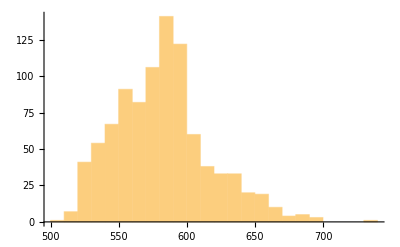

```mathematica
Histogram[ToExpression[DeleteCases[(If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],StringTake[#[[-1,-3]],-6],0]])&/@data1,_Integer]]]
```

```mathematica
newVisibleSpectrum=With[{colors={Image`ColorOperationsDump`$wavelengths,XYZColor@@@Image`ColorOperationsDump`tris}ᵀ},Blend[colors,#]&];
```

Transpose::nmtx: The first two levels of {Image`ColorOperationsDump`$wavelengths,Image`ColorOperationsDump`tris} cannot be transposed.

```mathematica
Count[x,True]
```

715

```mathematica
Count[x, False]
```

223

```mathematica
data2= Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_originalmesh_10x_10000.csv"],{2}];
output2= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],4,3],If[Count[StringTake[#[[All,-1]],{-2}],"5"]>0,If[Count[StringTake[#[[All,-1]],{-2}],"5"]>1,7,6],5]]])&/@data2;
chart2=Table[Count[output2,i],{i,0,7}]
(*energychart1={TotalUsedEnergy[data1], TotalUntouchedEnergy[data1],TotalEscapedEnergy[data1],TotalEnergy[data1]-TotalOutput[data1]}*)
PieChart[chart2,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Hit target but wrong wavelength", "Useful", "Absorbed by LC in first instance","Absorbed by LC after one emission", "Absorbed by LC after multiple emissions"}, ChartStyle->"DarkRainbow"]
(*PieChart[energychart1,ChartLegends->{"Output", "Untouched", "Escaped", "Lost"}, ChartStyle->{Yellow,Green, Blue, Gray}]*)
```

{631,5151,1772,166,511,953,462,354}

-Graphics-

```mathematica
data2= Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_fishtailmesh_10000.csv"],{2}];
output2= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],4,3],If[Count[StringTake[#[[All,-1]],{-2}],"5"]>0,If[Count[StringTake[#[[All,-1]],{-2}],"5"]>1,7,6],5]]])&/@data2;
chart2=Table[Count[output2,i],{i,0,7}]
(*energychart1={TotalUsedEnergy[data1], TotalUntouchedEnergy[data1],TotalEscapedEnergy[data1],TotalEnergy[data1]-TotalOutput[data1]}*)
PieChart[chart2,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Hit target but wrong wavelength", "Useful", "Absorbed by LC in first instance","Absorbed by LC after one emission", "Absorbed by LC after multiple emissions"}, ChartStyle->"DarkRainbow"]
(*PieChart[energychart1,ChartLegends->{"Output", "Untouched", "Escaped", "Lost"}, ChartStyle->{Yellow,Green, Blue, Gray}]*)
```

{5175,3244,424,73,229,529,212,114}

-Graphics-

```mathematica
data2= Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_fishtailcurvemesh_10000.csv"],{2}];
output2= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],4,3],If[Count[StringTake[#[[All,-1]],{-2}],"5"]>0,If[Count[StringTake[#[[All,-1]],{-2}],"5"]>1,7,6],5]]])&/@data2;
chart2=Table[Count[output2,i],{i,0,7}]
(*energychart1={TotalUsedEnergy[data1], TotalUntouchedEnergy[data1],TotalEscapedEnergy[data1],TotalEnergy[data1]-TotalOutput[data1]}*)
PieChart[chart2,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Hit target but wrong wavelength", "Useful", "Absorbed by LC in first instance","Absorbed by LC after one emission", "Absorbed by LC after multiple emissions"}, ChartStyle->"DarkRainbow"]
(*PieChart[energychart1,ChartLegends->{"Output", "Untouched", "Escaped", "Lost"}, ChartStyle->{Yellow,Green, Blue, Gray}]*)
```

{5877,2118,1072,72,273,357,149,82}

-Graphics-

```mathematica
data2= Map[CleanOutput,Import["C:\\Users\\seif\\Downloads\\ceyag_lumi_wedge\\ceyag_lumi_wedge\\output_air_withPLQY_fishtailcurvemesh_10000.csv"],{2}];
output2= (If[StringTake[#[[-1,-1]],{-2}]=="6",
If[Length[#]==2,0,
If[AnyTrue[StringTake[#[[All,-1]],{-2}],#=="5"&],1,2]],
If[CheckSphere[(RemovePosition[#]&/@#[[-1,1;;3]])],If[Between[ToExpression[StringTake[#[[-1,-3]],-6]],{450,600}],4,3],If[Count[StringTake[#[[All,-1]],{-2}],"5"]>0,If[Count[StringTake[#[[All,-1]],{-2}],"5"]>1,7,6],5]]])&/@data2;
chart2=Table[Count[output2,i],{i,0,7}]
(*energychart1={TotalUsedEnergy[data1], TotalUntouchedEnergy[data1],TotalEscapedEnergy[data1],TotalEnergy[data1]-TotalOutput[data1]}*)
PieChart[chart2,ChartLegends->{"No interaction", "Luminescence but escaped", "Transmitted without fluoresence", "Hit target but wrong wavelength", "Useful", "Absorbed by LC in first instance","Absorbed by LC after one emission", "Absorbed by LC after multiple emissions"}, ChartStyle->"DarkRainbow"]
```